```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.2,Jtwo,-0.1,z]-G22[1,0.2,Jtwo,-0.1,z]-G12[1,0.2,Jtwo,-0.1,z]^2+G11[1,0.2,Jtwo,-0.1,z]G22[1,0.2,Jtwo,-0.1,z]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[-1,-0.0005,0.7536715765093541]]
```

{{-0.005,0.748483},{-0.01,0.743114},{-0.015,0.737576},{-0.02,0.731879},{-0.025,0.726033},{-0.03,0.720046},{-0.035,0.713924},{-0.04,0.707673},{-0.045,0.701298},{-0.05,0.694803},{-0.055,0.68819},{-0.06,0.681461},{-0.065,0.67462},{-0.07,0.667666},{-0.075,0.660599},{-0.08,0.653421},{-0.085,0.646131},{-0.09,0.638728},{-0.095,0.63121},{-0.1,0.623576}}

```mathematica
moduler[Lister[1,0.0005,0.7536715765093541]]
```

{{0.005,0.758665},{0.01,0.763448},{0.015,0.768003},{0.02,0.772313},{0.025,0.776357},{0.03,0.780115},{0.035,0.783565},{0.04,0.786687},{0.045,0.789461},{0.05,0.79187},{0.055,0.793898},{0.06,0.795536},{0.065,0.796776},{0.07,0.797616},{0.075,0.798058},{0.08,0.798109},{0.085,0.797779},{0.09,0.797081},{0.095,0.796031},{0.1,0.794646}}

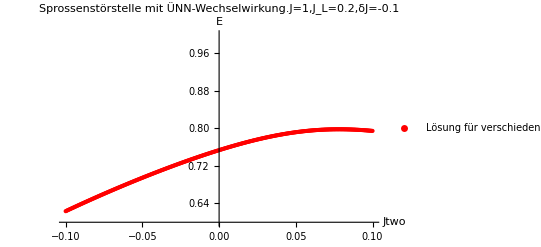

```mathematica
P = ListPlot[Fueger[moduler[Lister[-1,-0.0005,0.7536715765093541]],moduler[Lister[1,0.0005,0.7536715765093541]]],AxesLabel->{Jtwo,"E"},PlotRange->{0.6,1},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.2,δJ=-0.1",PlotStyle->Red]
```

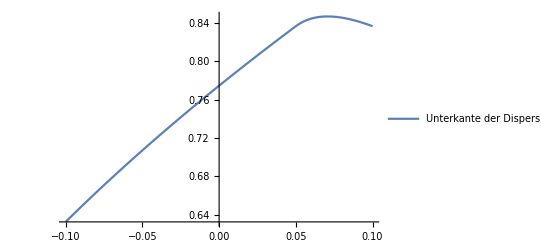

```mathematica
G = Plot[Sqrt[1+2(0.2*Cos[Inv[0.2,J]]+J*Cos[2*Inv[0.2,J]])],{J,-0.1,0.1},PlotLegends->{"Unterkante der Dispersion"}]
```

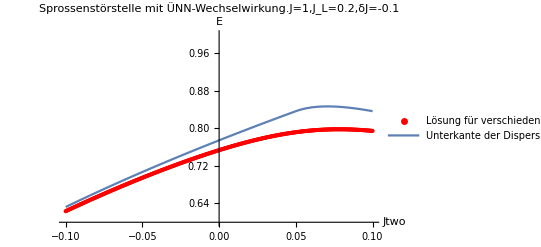

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.2,moduler[Lister[-1,-0.005,0.7536715765093541]]]
```

{{-0.005,0.0196312},{-0.01,0.0184632},{-0.015,0.0174077},{-0.02,0.0164525},{-0.025,0.0155868},{-0.03,0.014801},{-0.035,0.0140869},{-0.04,0.0134369},{-0.045,0.0128446},{-0.05,0.012304},{-0.055,0.0118103},{-0.06,0.0113589},{-0.065,0.0109457},{-0.07,0.0105675},{-0.075,0.010221},{-0.08,0.00990348},{-0.085,0.0096126},{-0.09,0.0093462},{-0.095,0.00910237},{-0.1,0.00887942}}

```mathematica
differ[1,0.2,moduler[Lister[1,0.005,0.7536715765093541]]]
```

{{0.005,0.0223601},{0.01,0.0239531},{0.015,0.0257221},{0.02,0.027687},{0.025,0.0298688},{0.03,0.0322893},{0.035,0.0349706},{0.04,0.0379345},{0.045,0.0412016},{0.05,0.432875},{0.055,0.0476371},{0.06,0.0490547},{0.065,0.049483},{0.07,0.0492273},{0.075,0.048504},{0.08,0.0474681},{0.085,0.0462314},{0.09,0.0448744},{0.095,0.0434548},{0.1,0.0420138}}

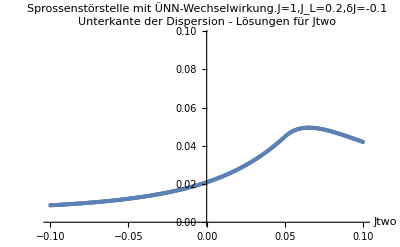

```mathematica
ListPlot[Fueger[differ[-1,0.2,moduler[Lister[-1,-0.0005,0.7536715765093541]]],differ[1,0.2,moduler[Lister[1,0.0005,0.7536715765093541]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.2,δJ=-0.1"]
```

```mathematica
Maxfinder[list_] := Module[{gross=0,spot=0},
Do[
If[list[[n,2]]>gross,spot=list[[n,1]]];
If[list[[n,2]]>gross,gross=list[[n,2]]];
,{n,1,400,1}];
{spot,gross}
]
```

```mathematica
Maxfinder[Fueger[moduler[Lister[-1,-0.0005,0.7536715765093541]],moduler[Lister[1,0.0005,0.7536715765093541]]]]
```

{0.078,0.798135}

```mathematica
Fueger[moduler[Lister[-1,-0.0005,0.7536715765093541]],moduler[Lister[1,0.0005,0.7536715765093541]]]
```

{{-0.0005,0.753161},{-0.001,0.752649},{-0.0015,0.752135},{-0.002,0.751619},{-0.0025,0.751101},{-0.003,0.750581},{-0.0035,0.750059},{-0.004,0.749536},{-0.0045,0.749011},{-0.005,0.748483},{-0.0055,0.747954},{-0.006,0.747424},{-0.0065,0.746891},{-0.007,0.746357},{-0.0075,0.745821},{-0.008,0.745283},{-0.0085,0.744743},{-0.009,0.744202},{-0.0095,0.743659},{-0.01,0.743114},{-0.0105,0.742568},{-0.011,0.74202},{-0.0115,0.74147},{-0.012,0.740918},{-0.0125,0.740365},{-0.013,0.739811},{-0.0135,0.739254},{-0.014,0.738696},{-0.0145,0.738137},{-0.015,0.737576},{-0.0155,0.737013},{-0.016,0.736449},{-0.0165,0.735883},{-0.017,0.735316},{-0.0175,0.734747},{-0.018,0.734176},{-0.0185,0.733604},{-0.019,0.733031},{-0.0195,0.732456},{-0.02,0.731879},{-0.0205,0.731301},{-0.021,0.730721},{-0.0215,0.730141},{-0.022,0.729558},{-0.0225,0.728974},{-0.023,0.728389},{-0.0235,0.727802},{-0.024,0.727214},{-0.0245,0.726624},{-0.025,0.726033},{-0.0255,0.725441},{-0.026,0.724847},{-0.0265,0.724251},{-0.027,0.723655},{-0.0275,0.723057},{-0.028,0.722457},{-0.0285,0.721856},{-0.029,0.721254},{-0.0295,0.720651},{-0.03,0.720046},{-0.0305,0.71944},{-0.031,0.718832},{-0.0315,0.718223},{-0.032,0.717613},{-0.0325,0.717001},{-0.033,0.716389},{-0.0335,0.715774},{-0.034,0.715159},{-0.0345,0.714542},{-0.035,0.713924},{-0.0355,0.713305},{-0.036,0.712684},{-0.0365,0.712062},{-0.037,0.711439},{-0.0375,0.710815},{-0.038,0.710189},{-0.0385,0.709562},{-0.039,0.708934},{-0.0395,0.708304},{-0.04,0.707673},{-0.0405,0.707041},{-0.041,0.706408},{-0.0415,0.705774},{-0.042,0.705138},{-0.0425,0.704501},{-0.043,0.703863},{-0.0435,0.703224},{-0.044,0.702583},{-0.0445,0.701941},{-0.045,0.701298},{-0.0455,0.700654},{-0.046,0.700009},{-0.0465,0.699362},{-0.047,0.698714},{-0.0475,0.698065},{-0.048,0.697415},{-0.0485,0.696764},{-0.049,0.696111},{-0.0495,0.695458},{-0.05,0.694803},{-0.0505,0.694147},{-0.051,0.693489},{-0.0515,0.692831},{-0.052,0.692171},{-0.0525,0.691511},{-0.053,0.690849},{-0.0535,0.690186},{-0.054,0.689522},{-0.0545,0.688856},{-0.055,0.68819},{-0.0555,0.687522},{-0.056,0.686853},{-0.0565,0.686183},{-0.057,0.685512},{-0.0575,0.68484},{-0.058,0.684166},{-0.0585,0.683492},{-0.059,0.682816},{-0.0595,0.682139},{-0.06,0.681461},{-0.0605,0.680782},{-0.061,0.680102},{-0.0615,0.679421},{-0.062,0.678738},{-0.0625,0.678055},{-0.063,0.67737},{-0.0635,0.676684},{-0.064,0.675997},{-0.0645,0.675309},{-0.065,0.67462},{-0.0655,0.673929},{-0.066,0.673238},{-0.0665,0.672545},{-0.067,0.671851},{-0.0675,0.671157},{-0.068,0.670461},{-0.0685,0.669764},{-0.069,0.669065},{-0.0695,0.668366},{-0.07,0.667666},{-0.0705,0.666964},{-0.071,0.666261},{-0.0715,0.665557},{-0.072,0.664853},{-0.0725,0.664146},{-0.073,0.663439},{-0.0735,0.662731},{-0.074,0.662022},{-0.0745,0.661311},{-0.075,0.660599},{-0.0755,0.659887},{-0.076,0.659173},{-0.0765,0.658458},{-0.077,0.657742},{-0.0775,0.657024},{-0.078,0.656306},{-0.0785,0.655587},{-0.079,0.654866},{-0.0795,0.654144},{-0.08,0.653421},{-0.0805,0.652698},{-0.081,0.651972},{-0.0815,0.651246},{-0.082,0.650519},{-0.0825,0.64979},{-0.083,0.649061},{-0.0835,0.64833},{-0.084,0.647598},{-0.0845,0.646865},{-0.085,0.646131},{-0.0855,0.645396},{-0.086,0.64466},{-0.0865,0.643922},{-0.087,0.643184},{-0.0875,0.642444},{-0.088,0.641703},{-0.0885,0.640961},{-0.089,0.640218},{-0.0895,0.639473},{-0.09,0.638728},{-0.0905,0.637981},{-0.091,0.637234},{-0.0915,0.636485},{-0.092,0.635735},{-0.0925,0.634983},{-0.093,0.634231},{-0.0935,0.633478},{-0.094,0.632723},{-0.0945,0.631967},{-0.095,0.63121},{-0.0955,0.630452},{-0.096,0.629693},{-0.0965,0.628932},{-0.097,0.628171},{-0.0975,0.627408},{-0.098,0.626644},{-0.0985,0.625879},{-0.099,0.625112},{-0.0995,0.624345},{-0.1,0.623576},{0.0005,0.75418},{0.001,0.754686},{0.0015,0.755191},{0.002,0.755693},{0.0025,0.756193},{0.003,0.756692},{0.0035,0.757188},{0.004,0.757682},{0.0045,0.758175},{0.005,0.758665},{0.0055,0.759153},{0.006,0.759639},{0.0065,0.760123},{0.007,0.760604},{0.0075,0.761084},{0.008,0.761561},{0.0085,0.762036},{0.009,0.762509},{0.0095,0.762979},{0.01,0.763448},{0.0105,0.763914},{0.011,0.764378},{0.0115,0.764839},{0.012,0.765298},{0.0125,0.765755},{0.013,0.76621},{0.0135,0.766662},{0.014,0.767111},{0.0145,0.767558},{0.015,0.768003},{0.0155,0.768446},{0.016,0.768886},{0.0165,0.769323},{0.017,0.769758},{0.0175,0.77019},{0.018,0.77062},{0.0185,0.771047},{0.019,0.771472},{0.0195,0.771894},{0.02,0.772313},{0.0205,0.77273},{0.021,0.773144},{0.0215,0.773555},{0.022,0.773964},{0.0225,0.774369},{0.023,0.774773},{0.0235,0.775173},{0.024,0.77557},{0.0245,0.775965},{0.025,0.776357},{0.0255,0.776746},{0.026,0.777132},{0.0265,0.777515},{0.027,0.777896},{0.0275,0.778273},{0.028,0.778647},{0.0285,0.779019},{0.029,0.779387},{0.0295,0.779752},{0.03,0.780115},{0.0305,0.780474},{0.031,0.78083},{0.0315,0.781183},{0.032,0.781533},{0.0325,0.781879},{0.033,0.782223},{0.0335,0.782563},{0.034,0.7829},{0.0345,0.783234},{0.035,0.783565},{0.0355,0.783892},{0.036,0.784216},{0.0365,0.784537},{0.037,0.784854},{0.0375,0.785168},{0.038,0.785479},{0.0385,0.785786},{0.039,0.786089},{0.0395,0.78639},{0.04,0.786687},{0.0405,0.78698},{0.041,0.78727},{0.0415,0.787556},{0.042,0.787839},{0.0425,0.788118},{0.043,0.788394},{0.0435,0.788666},{0.044,0.788935},{0.0445,0.7892},{0.045,0.789461},{0.0455,0.789718},{0.046,0.789972},{0.0465,0.790222},{0.047,0.790469},{0.0475,0.790712},{0.048,0.790951},{0.0485,0.791186},{0.049,0.791418},{0.0495,0.791646},{0.05,0.79187},{0.0505,0.79209},{0.051,0.792306},{0.0515,0.792519},{0.052,0.792727},{0.0525,0.792932},{0.053,0.793133},{0.0535,0.79333},{0.054,0.793524},{0.0545,0.793713},{0.055,0.793898},{0.0555,0.79408},{0.056,0.794257},{0.0565,0.794431},{0.057,0.794601},{0.0575,0.794766},{0.058,0.794928},{0.0585,0.795086},{0.059,0.79524},{0.0595,0.79539},{0.06,0.795536},{0.0605,0.795678},{0.061,0.795816},{0.0615,0.79595},{0.062,0.79608},{0.0625,0.796206},{0.063,0.796328},{0.0635,0.796446},{0.064,0.79656},{0.0645,0.79667},{0.065,0.796776},{0.0655,0.796878},{0.066,0.796976},{0.0665,0.79707},{0.067,0.79716},{0.0675,0.797246},{0.068,0.797328},{0.0685,0.797406},{0.069,0.79748},{0.0695,0.79755},{0.07,0.797616},{0.0705,0.797678},{0.071,0.797736},{0.0715,0.79779},{0.072,0.79784},{0.0725,0.797886},{0.073,0.797928},{0.0735,0.797966},{0.074,0.798001},{0.0745,0.798031},{0.075,0.798058},{0.0755,0.79808},{0.076,0.798099},{0.0765,0.798114},{0.077,0.798124},{0.0775,0.798131},{0.078,0.798135},{0.0785,0.798134},{0.079,0.798129},{0.0795,0.798121},{0.08,0.798109},{0.0805,0.798093},{0.081,0.798073},{0.0815,0.798049},{0.082,0.798022},{0.0825,0.79799},{0.083,0.797956},{0.0835,0.797917},{0.084,0.797875},{0.0845,0.797828},{0.085,0.797779},{0.0855,0.797725},{0.086,0.797668},{0.0865,0.797607},{0.087,0.797543},{0.0875,0.797475},{0.088,0.797403},{0.0885,0.797328},{0.089,0.797249},{0.0895,0.797167},{0.09,0.797081},{0.0905,0.796992},{0.091,0.796899},{0.0915,0.796802},{0.092,0.796702},{0.0925,0.796599},{0.093,0.796492},{0.0935,0.796382},{0.094,0.796269},{0.0945,0.796152},{0.095,0.796031},{0.0955,0.795908},{0.096,0.79578},{0.0965,0.79565},{0.097,0.795516},{0.0975,0.79538},{0.098,0.795239},{0.0985,0.795096},{0.099,0.794949},{0.0995,0.794799},{0.1,0.794646}}

```mathematica
Fueger[differ[-1,0.2,moduler[Lister[-1,-0.0005,0.7536715765093541]]],differ[1,0.2,moduler[Lister[1,0.0005,0.7536715765093541]]]]
```

{{-0.0005,0.0207896},{-0.001,0.0206555},{-0.0015,0.0205228},{-0.002,0.0203915},{-0.0025,0.0202615},{-0.003,0.0201328},{-0.0035,0.0200055},{-0.004,0.0198794},{-0.0045,0.0197547},{-0.005,0.0196312},{-0.0055,0.0195089},{-0.006,0.019388},{-0.0065,0.0192682},{-0.007,0.0191497},{-0.0075,0.0190323},{-0.008,0.0189162},{-0.0085,0.0188012},{-0.009,0.0186874},{-0.0095,0.0185748},{-0.01,0.0184632},{-0.0105,0.0183528},{-0.011,0.0182435},{-0.0115,0.0181353},{-0.012,0.0180282},{-0.0125,0.0179222},{-0.013,0.0178172},{-0.0135,0.0177133},{-0.014,0.0176104},{-0.0145,0.0175086},{-0.015,0.0174077},{-0.0155,0.0173079},{-0.016,0.017209},{-0.0165,0.0171111},{-0.017,0.0170142},{-0.0175,0.0169183},{-0.018,0.0168232},{-0.0185,0.0167292},{-0.019,0.016636},{-0.0195,0.0165438},{-0.02,0.0164525},{-0.0205,0.016362},{-0.021,0.0162725},{-0.0215,0.0161838},{-0.022,0.016096},{-0.0225,0.016009},{-0.023,0.0159229},{-0.0235,0.0158377},{-0.024,0.0157532},{-0.0245,0.0156696},{-0.025,0.0155868},{-0.0255,0.0155047},{-0.026,0.0154235},{-0.0265,0.015343},{-0.027,0.0152634},{-0.0275,0.0151844},{-0.028,0.0151063},{-0.0285,0.0150289},{-0.029,0.0149522},{-0.0295,0.0148763},{-0.03,0.014801},{-0.0305,0.0147265},{-0.031,0.0146527},{-0.0315,0.0145796},{-0.032,0.0145072},{-0.0325,0.0144355},{-0.033,0.0143645},{-0.0335,0.0142941},{-0.034,0.0142244},{-0.0345,0.0141553},{-0.035,0.0140869},{-0.0355,0.0140191},{-0.036,0.013952},{-0.0365,0.0138855},{-0.037,0.0138196},{-0.0375,0.0137543},{-0.038,0.0136897},{-0.0385,0.0136256},{-0.039,0.0135621},{-0.0395,0.0134992},{-0.04,0.0134369},{-0.0405,0.0133752},{-0.041,0.013314},{-0.0415,0.0132534},{-0.042,0.0131934},{-0.0425,0.0131339},{-0.043,0.013075},{-0.0435,0.0130166},{-0.044,0.0129587},{-0.0445,0.0129014},{-0.045,0.0128446},{-0.0455,0.0127883},{-0.046,0.0127325},{-0.0465,0.0126772},{-0.047,0.0126224},{-0.0475,0.0125682},{-0.048,0.0125144},{-0.0485,0.0124611},{-0.049,0.0124083},{-0.0495,0.0123559},{-0.05,0.012304},{-0.0505,0.0122526},{-0.051,0.0122017},{-0.0515,0.0121512},{-0.052,0.0121012},{-0.0525,0.0120516},{-0.053,0.0120025},{-0.0535,0.0119538},{-0.054,0.0119055},{-0.0545,0.0118577},{-0.055,0.0118103},{-0.0555,0.0117633},{-0.056,0.0117168},{-0.0565,0.0116706},{-0.057,0.0116249},{-0.0575,0.0115796},{-0.058,0.0115346},{-0.0585,0.0114901},{-0.059,0.011446},{-0.0595,0.0114022},{-0.06,0.0113589},{-0.0605,0.0113159},{-0.061,0.0112733},{-0.0615,0.0112311},{-0.062,0.0111892},{-0.0625,0.0111477},{-0.063,0.0111066},{-0.0635,0.0110659},{-0.064,0.0110255},{-0.0645,0.0109854},{-0.065,0.0109457},{-0.0655,0.0109064},{-0.066,0.0108674},{-0.0665,0.0108287},{-0.067,0.0107904},{-0.0675,0.0107525},{-0.068,0.0107148},{-0.0685,0.0106775},{-0.069,0.0106405},{-0.0695,0.0106038},{-0.07,0.0105675},{-0.0705,0.0105314},{-0.071,0.0104957},{-0.0715,0.0104603},{-0.072,0.0104252},{-0.0725,0.0103904},{-0.073,0.0103559},{-0.0735,0.0103217},{-0.074,0.0102879},{-0.0745,0.0102543},{-0.075,0.010221},{-0.0755,0.0101879},{-0.076,0.0101552},{-0.0765,0.0101228},{-0.077,0.0100906},{-0.0775,0.0100587},{-0.078,0.0100271},{-0.0785,0.00999582},{-0.079,0.00996477},{-0.0795,0.00993399},{-0.08,0.00990348},{-0.0805,0.00987323},{-0.081,0.00984325},{-0.0815,0.00981352},{-0.082,0.00978406},{-0.0825,0.00975485},{-0.083,0.0097259},{-0.0835,0.0096972},{-0.084,0.00966876},{-0.0845,0.00964056},{-0.085,0.0096126},{-0.0855,0.0095849},{-0.086,0.00955743},{-0.0865,0.00953021},{-0.087,0.00950322},{-0.0875,0.00947647},{-0.088,0.00944995},{-0.0885,0.00942367},{-0.089,0.00939762},{-0.0895,0.0093718},{-0.09,0.0093462},{-0.0905,0.00932083},{-0.091,0.00929569},{-0.0915,0.00927076},{-0.092,0.00924606},{-0.0925,0.00922157},{-0.093,0.0091973},{-0.0935,0.00917325},{-0.094,0.00914941},{-0.0945,0.00912579},{-0.095,0.00910237},{-0.0955,0.00907916},{-0.096,0.00905616},{-0.0965,0.00903336},{-0.097,0.00901077},{-0.0975,0.00898838},{-0.098,0.00896619},{-0.0985,0.00894421},{-0.099,0.00892242},{-0.0995,0.00890082},{-0.1,0.00887942},{0.0005,0.021062},{0.001,0.0212003},{0.0015,0.0213401},{0.002,0.0214813},{0.0025,0.021624},{0.003,0.0217682},{0.0035,0.0219138},{0.004,0.0220611},{0.0045,0.0222098},{0.005,0.0223601},{0.0055,0.022512},{0.006,0.0226655},{0.0065,0.0228206},{0.007,0.0229774},{0.0075,0.0231358},{0.008,0.0232958},{0.0085,0.0234576},{0.009,0.023621},{0.0095,0.0237862},{0.01,0.0239531},{0.0105,0.0241217},{0.011,0.0242922},{0.0115,0.0244644},{0.012,0.0246385},{0.0125,0.0248144},{0.013,0.0249921},{0.0135,0.0251717},{0.014,0.0253533},{0.0145,0.0255367},{0.015,0.0257221},{0.0155,0.0259094},{0.016,0.0260988},{0.0165,0.0262901},{0.017,0.0264834},{0.0175,0.0266788},{0.018,0.0268762},{0.0185,0.0270758},{0.019,0.0272774},{0.0195,0.0274811},{0.02,0.027687},{0.0205,0.0278951},{0.021,0.0281054},{0.0215,0.0283178},{0.022,0.0285325},{0.0225,0.0287495},{0.023,0.0289687},{0.0235,0.0291902},{0.024,0.0294141},{0.0245,0.0296403},{0.025,0.0298688},{0.0255,0.0300998},{0.026,0.0303331},{0.0265,0.0305689},{0.027,0.0308072},{0.0275,0.0310479},{0.028,0.0312911},{0.0285,0.0315368},{0.029,0.0317851},{0.0295,0.0320359},{0.03,0.0322893},{0.0305,0.0325453},{0.031,0.032804},{0.0315,0.0330653},{0.032,0.0333293},{0.0325,0.033596},{0.033,0.0338654},{0.0335,0.0341375},{0.034,0.0344124},{0.0345,0.0346901},{0.035,0.0349706},{0.0355,0.0352539},{0.036,0.0355401},{0.0365,0.0358291},{0.037,0.0361211},{0.0375,0.0364159},{0.038,0.0367137},{0.0385,0.0370144},{0.039,0.0373181},{0.0395,0.0376248},{0.04,0.0379345},{0.0405,0.0382473},{0.041,0.0385631},{0.0415,0.0388819},{0.042,0.0392039},{0.0425,0.039529},{0.043,0.0398572},{0.0435,0.0401885},{0.044,0.040523},{0.0445,0.0408607},{0.045,0.0412016},{0.0455,0.0415457},{0.046,0.0418931},{0.0465,0.0422437},{0.047,0.0425976},{0.0475,0.0429548},{0.048,0.0433153},{0.0485,0.0436791},{0.049,0.0440462},{0.0495,0.0444167},{0.05,0.432875},{0.0505,0.0451559},{0.051,0.0455015},{0.0515,0.0458281},{0.052,0.0461364},{0.0525,0.046427},{0.053,0.0467006},{0.0535,0.0469578},{0.054,0.0471993},{0.0545,0.0474255},{0.055,0.0476371},{0.0555,0.0478346},{0.056,0.0480185},{0.0565,0.0481892},{0.057,0.0483473},{0.0575,0.0484932},{0.058,0.0486274},{0.0585,0.0487502},{0.059,0.0488621},{0.0595,0.0489635},{0.06,0.0490547},{0.0605,0.0491362},{0.061,0.0492082},{0.0615,0.0492711},{0.062,0.0493252},{0.0625,0.0493709},{0.063,0.0494085},{0.0635,0.0494382},{0.064,0.0494603},{0.0645,0.0494752},{0.065,0.049483},{0.0655,0.049484},{0.066,0.0494786},{0.0665,0.0494668},{0.067,0.049449},{0.0675,0.0494254},{0.068,0.0493962},{0.0685,0.0493616},{0.069,0.0493217},{0.0695,0.0492769},{0.07,0.0492273},{0.0705,0.0491731},{0.071,0.0491143},{0.0715,0.0490514},{0.072,0.0489843},{0.0725,0.0489132},{0.073,0.0488384},{0.0735,0.0487599},{0.074,0.0486779},{0.0745,0.0485926},{0.075,0.048504},{0.0755,0.0484123},{0.076,0.0483177},{0.0765,0.0482203},{0.077,0.0481201},{0.0775,0.0480173},{0.078,0.047912},{0.0785,0.0478044},{0.079,0.0476944},{0.0795,0.0475823},{0.08,0.0474681},{0.0805,0.0473519},{0.081,0.0472339},{0.0815,0.047114},{0.082,0.0469924},{0.0825,0.0468692},{0.083,0.0467444},{0.0835,0.0466182},{0.084,0.0464906},{0.0845,0.0463616},{0.085,0.0462314},{0.0855,0.0461},{0.086,0.0459675},{0.0865,0.0458339},{0.087,0.0456994},{0.0875,0.0455639},{0.088,0.0454275},{0.0885,0.0452903},{0.089,0.0451524},{0.0895,0.0450137},{0.09,0.0448744},{0.0905,0.0447344},{0.091,0.044594},{0.0915,0.0444529},{0.092,0.0443114},{0.0925,0.0441695},{0.093,0.0440272},{0.0935,0.0438846},{0.094,0.0437416},{0.0945,0.0435983},{0.095,0.0434548},{0.0955,0.0433111},{0.096,0.0431673},{0.0965,0.0430233},{0.097,0.0428792},{0.0975,0.042735},{0.098,0.0425907},{0.0985,0.0424465},{0.099,0.0423022},{0.0995,0.042158},{0.1,0.0420138}}